```mathematica
$MinPrecision=53;
```

### Defining The Domains

#### u Domain(s)

```mathematica
prec=64;
```

```mathematica
uOuterMin=1/10;
uOuterMax= 11/10;
uOuterDomains=2;
uOuterNodes=24;
uInnerNodes=12;
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];
```

```mathematica
InterfaceNodes//N
```

{0.1,0.6,1.1}

```mathematica
{0.1,0.555,1.01}
```

{0.1,0.555,1.01}

```mathematica
1.01/36 0.4//N
```

0.0112222

```mathematica
GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]
```

```mathematica
uValues=GetuDomain[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

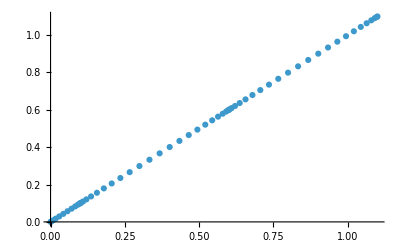

```mathematica
ListPlot[Transpose[{uValues,uValues}]]
```

#### x Domain

```mathematica
xMin=-5;
xMax=5;
L=xMax-xMin;
xNodes=100;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-5,-49/10,-24/5,-47/10,-23/5,-9/2,-22/5,-43/10,-21/5,-41/10,-4,-39/10,-19/5,-37/10,-18/5,-7/2,-17/5,-33/10,-16/5,-31/10,-3,-29/10,-14/5,-27/10,-13/5,-5/2,-12/5,-23/10,-11/5,-21/10,-2,-19/10,-9/5,-17/10,-8/5,-3/2,-7/5,-13/10,-6/5,-11/10,-1,-9/10,-4/5,-7/10,-3/5,-1/2,-2/5,-3/10,-1/5,-1/10,0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5,3/2,8/5,17/10,9/5,19/10,2,21/10,11/5,23/10,12/5,5/2,13/5,27/10,14/5,29/10,3,31/10,16/5,33/10,17/5,7/2,18/5,37/10,19/5,39/10,4,41/10,21/5,43/10,22/5,9/2,23/5,47/10,24/5,49/10}

```mathematica
Deltax^4//N
```

0.0001

#### y Domain

```mathematica
yMin=-5;
yMax=5;
yNodes=xNodes;
Deltay=Abs[yMin-yMax]/yNodes;
yValues=Table[yMin+i Deltay,{i,0,yNodes-1}];
```

```mathematica
yValues
```

{-5,-49/10,-24/5,-47/10,-23/5,-9/2,-22/5,-43/10,-21/5,-41/10,-4,-39/10,-19/5,-37/10,-18/5,-7/2,-17/5,-33/10,-16/5,-31/10,-3,-29/10,-14/5,-27/10,-13/5,-5/2,-12/5,-23/10,-11/5,-21/10,-2,-19/10,-9/5,-17/10,-8/5,-3/2,-7/5,-13/10,-6/5,-11/10,-1,-9/10,-4/5,-7/10,-3/5,-1/2,-2/5,-3/10,-1/5,-1/10,0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5,3/2,8/5,17/10,9/5,19/10,2,21/10,11/5,23/10,12/5,5/2,13/5,27/10,14/5,29/10,3,31/10,16/5,33/10,17/5,7/2,18/5,37/10,19/5,39/10,4,41/10,21/5,43/10,22/5,9/2,23/5,47/10,24/5,49/10}

#### Grid

```mathematica
MyGrid=Table[{uValues[[u]],xValues[[x]],yValues[[y]]},{u,1,uValues//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid//Dimensions
```

{58,100,100,3}

## Boosted Black Brain

## Inhomogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

#### Boosting

```mathematica
ClearAll[u1d,u0d,u2d]

u1d[x_,y_]:=0;
u2d[x_,y_]:=0;
b=1;
```

```mathematica
IDType="o1_A0d1";
IDFolderName="/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_"<>IDType<>"_L"<>ToString[xMax-xMin]<>"_"<>StringReplace[ToString[uOuterMin//N],"."->"d"]<>"ui"<>ToString[uInnerNodes]<>"_"<>ToString[uOuterDomains]<>"uo"<>ToString[uOuterNodes]<>"_N"<>ToString[xNodes]<>"_b"<>StringReplace[ToString[b//N],"."->"d"]<>"/k0_"<>IDType<>"_L"<>ToString[xMax-xMin]<>"_"<>StringReplace[ToString[uOuterMin//N],"."->"d"]<>"ui"<>ToString[uInnerNodes]<>"_"<>ToString[uOuterDomains]<>"uo"<>ToString[uOuterNodes]<>"_N"<>ToString[xNodes]<>"_b"<>StringReplace[ToString[b//N],"."->"d"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d

The horizon (b) has to be shifted by the energy computed in the masterscalar notebook (0.5013868846238644`). also, the 20 squared factor comes from the normalization factor used some 
paragraphs down.

```mathematica
uofρRule=DSolve[{D[u[ρ,x,y],{ρ}]==-u[ρ,x,y]^2(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1,x,y]==1*)},u,{ρ,x,y}]//Flatten;
```

```mathematica
c1Rule=Solve[C[1][x,y]==0(*uofρRule[[1,2]][1,x,y]==1*),C[1][x,y]]//Flatten;
```

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[1,1,2]]
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero

```mathematica
rofρ=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρ/.c1Rule//N
```

Function[{ρ,x,y},1/ρ+0.]

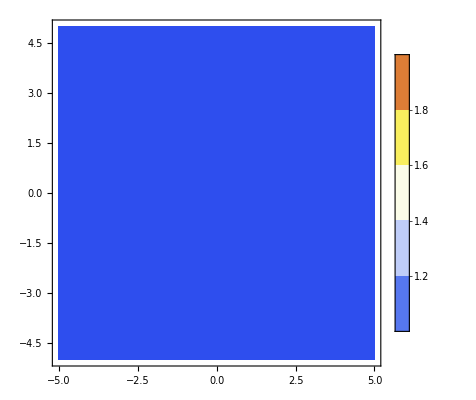

```mathematica
ContourPlot[rofρ[1,x,y]/.C[1][x,y]->0,{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap",MaxRecursion->5(*,PlotPoints->20*)]
```

```mathematica
(*result={c2->-0.12143028176015587866343211396646670584122480857360100464098635572301659734106`55.+2.9656373209623393738197615284868524325426624675530953267792147884984458659315`55. ⅈ,vty->6.94516266876838512434422329034088338715411459165227105553644017562362506671842`55.+4.21805293030637990021503816926660318235361012604515512115635265601693478600371`55. ⅈ,ω->3.20078892328591118308753668777941353539185477495863409577173595247294216788656`55.-4.90540243517292088583546808261898925054882991725144876951358768657415208061995`55. ⅈ};*)
```

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
ClearAll[uofρ]
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
uofρ=Function[{ρs,xs,ys},rofρ[[2]]^-1(*/.C[1][x,y]->0*)/.c1Rule[[1]]/.ρ->ρs/.x->xs/.y->ys]
```

Function[{ρs,xs,ys},1/rofρ⟦2⟧/.c1Rule⟦1⟧/.ρ→ρs/.x→xs/.y→ys]

Horizon location

```mathematica
Minimize[uofρ[b,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
Maximize[uofρ[b,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
```

1.

1.

```mathematica
Plot3D[uofρ[1,x,y],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic,(*PlotRange->All,*)(*MaxRecursion->4,*)ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
(*uofρToInt=ParallelTable[{MyGrid[[i,j,k]],uofρ[MyGrid[[i,j,k]][[1]],MyGrid[[i,j,k]][[2]],MyGrid[[i,j,k]][[3]]]},{i,1,MyGrid//Length},{j,1,MyGrid[[1]]//Length},{k,1,MyGrid[[1,1]]//Length}];//AbsoluteTiming*)
```

```mathematica
(*ρofuOld2=InverseFunction[Function[{ρ,x,y},Intuofρ[ρ,x,y]],1,3];*)
```

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ClearAll[ρofu,ρofu2]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
(*ρofu2=Function[C,ρofuOld2[C[[1]],C[[2]],C[[3]]]]*)
```

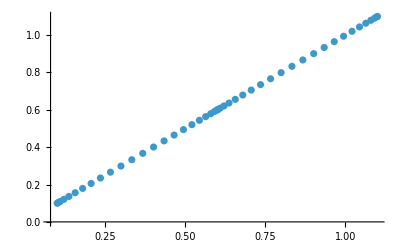

```mathematica
ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu[{uValues[[i]]//N,xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]
```

```mathematica
(*ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu2[{uValues[[i]],xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]*)
```

```mathematica
(*ParallelTable[ρofu2[MyGrid[[1,j,k]]](*,{i,1,uValues//Length}*),{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming*)
```

```mathematica
MyGrid//Dimensions
```

{58,100,100,3}

```mathematica
MyGrid//Dimensions
```

{58,100,100,3}

```mathematica
ρofu[MyGrid[[10,1,1]]];//AbsoluteTiming
ρofu[MyGrid[[10,3,10]]]
```

{0.000015,Null}

0.09206267664155905844309058244596838587566462492102689493213250588

```mathematica
OneRowρofuValues=ParallelTable[ρofu[MyGrid[[i,1,1]]],{i,1,uValues//Length}];//AbsoluteTiming
ρofuValues=Transpose[ParallelTable[OneRowρofuValues,{j,1,xValues//Length},{k,1,yValues//Length}],1];//AbsoluteTiming
```

{43.696,Null}

{5.47712,Null}

```mathematica
(*ρofuValues=ParallelTable[ρofu[MyGrid[[i,j,k]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming*)
```

```mathematica
MyGrid//Dimensions
ρofuValues2//Dimensions
```

{58,100,100,3}

{}

```mathematica
u1Values=Table[u1d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.007929,Null}

```mathematica
u2Values=Table[u2d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.005999,Null}

```mathematica
u0Values=Table[u0d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{3.24827,Null}

#### Perturbations

```mathematica
result={ϕvev->12.08495790317457930010330659033945317212768038838165608760252958040364205166499`55.+22.31288488912226043126393800258587359585529701404252228326401656658491137948547`55. ⅈ,ω->3.16125702750250084322854004662539373481491637459792946705864166658411532085278`55.-4.91641787967203611231623910219544407103262941017668626432597583562731859844265`55. ⅈ};
```

```mathematica
NormCoeff=0.1;
```

```mathematica
hxyFunctionNonNormalised[zz_,xx_,yy_]= 1/2 InterpolatingFunction[…][zz]/.v->0/.L->yMax-yMin/.result;
hxyNorm=MaxValue[hxyFunctionNonNormalised[zzz,0,0]//Abs,zzz>0&&zzz<1,zzz];
hxyFunction[zz_,xx_,yy_]:=NormCoeff hxyFunctionNonNormalised[zz,xx,yy]/hxyNorm;
```

Here we need to consider the definition of the perturbation in terms of the radial profile. In the nb where we compute the radial profile, we have h = e^(ikx_3-iωv)/(2 u^2)h(z),

```mathematica
Parametricgxy[u_,x_,y_]:=hxyFunction[u,x,y]//Re;
```

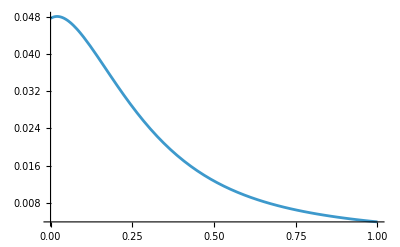

```mathematica
Plot[{Parametricgxy[u,xValues[[10]],yValues[[1]]]},{u,0,1.00},PlotRange->All]
```

The third equations has to include the complete perturbation as “a”

```mathematica
BulkFunctions=Solve[{S^2 E^(-u^3 Bin)Cosh[u^3 Gin]==u^-2,S^2 E^(u^3 Bin)Cosh[u^3 Gin]==u^-2,S^2 Sinh[u^3 Gin]==(*u^-2*)u a},{S,Gin,Bin}][[1]]/. C[1]->0/. C[2]->0/.C[3]->0
```

{S→-((1-a^2 u^6)^(1/4))/u,Gin→Log[(-√(1-a^2 u^6)-a u^3 √(1-a^2 u^6))/(-1+a^2 u^6)]/u^3,Bin→0}

```mathematica
{S->-((1-a^2)^(1/4))/u,Gin->Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^3,Bin->0}
```

{S→-((1-a^2)^(1/4))/u,Gin→Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^3,Bin→0}

```mathematica
{S->-((1-a^2)^(1/6))/u,Gin->Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4,B1in->0,B2in->-Log[(1-a^2)^(1/6)]/u^4}//TeXForm
```

\left\{S\to -\frac{\sqrt[6]{1-a^2}}{u},\text{Gin}\to \frac{\log \left(\frac{-\sqrt{1-a^2} a-\sqrt{1-a^2}}{a^2-1}\right)}{u^4},\text{B1in}\to
   0,\text{B2in}\to -\frac{\log \left(\sqrt[6]{1-a^2}\right)}{u^4}\right\}

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp(*/.ξ->Function[{t,z,y},0]*)//Series[#,{u,0,2}]&
```

1/u^2+(2 ξ[t,x,y])/u+(ξ[t,x,y]^2-2 ξ^(1,0,0)[t,x,y])+a3[t,0,x,y] u+a3^(0,1,0,0)[t,0,x,y] u^2+O[u]^3

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

```mathematica
AToMatch=u^-2(1-(b u)^3(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/u^2-u

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

Let' s look for ξ

Does this work with order term (it has to be checked for every configuration)???

```mathematica
(*SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule*)
```

xi can’t depend on t

```mathematica
Coefficient[AToMatch,u]
```

-1

```mathematica
Coefficient[AExpOfρ,u]
```

a3[t,0,x,y]

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,u]==Coefficient[AExpOfρ,u],a3[t,0,x,y]][[1]]
```

{a3[t,0,x,y]→-1}

```mathematica
xiRule=Solve[Coefficient[AExpOfρ,1/u]==Coefficient[AToMatch,1/u],  ξ[t,x,y]]//Flatten
```

{ξ[t,x,y]→0}

From Chasler paper a3 should be

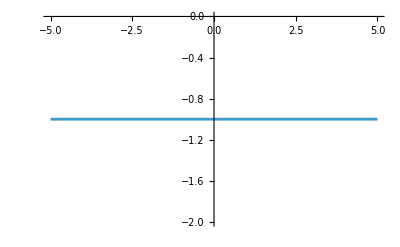

```mathematica
Plot[{(*-1/2(-1+27 u0d[0.59,y]^2)//Simplify,*)a3[t,0,x,y]/.a3Rule/.x->0.59},{y,-5,5}]
```

Export a3 Initial data

```mathematica
a3Data=Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
xiData=Table[(ξ[t,x,y](*/.ξ[t,x,y]->0*)(*1-Hypergeometric2F1[-0.3333333333333333,0.5,0.6666666666666666,-1/2-1/2 Cos[(2223497 y)/5898008975]]*)/.xiRule/.c1Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
guessDatarow=Table[N[(uofρRule[[1,2]][b^-1,x,y])^-1/.c1Rule/.x->xValues[[1]]/.y->yValues[[j]],prec]1(*,{i,1,xValues//Length}*),{j,1,yValues//Length}];//AbsoluteTiming
guessData=Table[guessDatarow,xValues//Length];
```

{0.000591,Null}

```mathematica
a3AttributesAndData={"a3"->a3Data};
xiAttributesAndData={"xi"->xiData};
guessAttributesAndData={"guess"->guessData};
```

```mathematica
Export[IDFolderName<>"Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1dInitiala3_BBB.h5

```mathematica
Export[IDFolderName<>"Initialxi_BBB.h5",xiAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1dInitialxi_BBB.h5

```mathematica
Export[IDFolderName<>"Initialguess_BBB.h5",guessAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1dInitialguess_BBB.h5

```mathematica
Import[IDFolderName<>"Initiala3_BBB.h5","Data"]//Keys
```

{/a3}

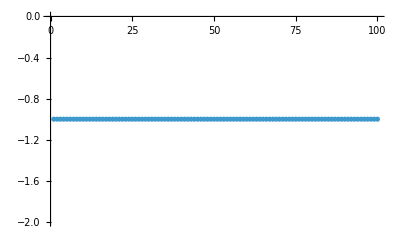

```mathematica
ListPlot[Import[IDFolderName<>"Initiala3_BBB.h5","Data"][[1,1]]]
```

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,x,y]+Derivative[0,1,0][ξ][t,x,y];
```

```mathematica
FExpOfρ=FExp
```

u f1[t,x,y]+ξ^(0,1,0)[t,x,y]

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
FToMatch=(*1/NormCoeff*)(*Ayy vty  z^4 E^(I k y)/(2 z^2)/.v->0/.k->2 Pi/L/.result//Re//Simplify*)-(b u(*ofu[{0,x,y}]*))^3/(u(*ofu[{0,x,y}]*))^2 u0d[x,y] u1d[x,y]
```

0

```mathematica
Ayy
```

Ayy

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fxRule=Solve[Coefficient[FToMatch,u]==Coefficient[FExpOfρ,u],f1[t,x,y]]//Simplify
```

{{f1[t,x,y]→0}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

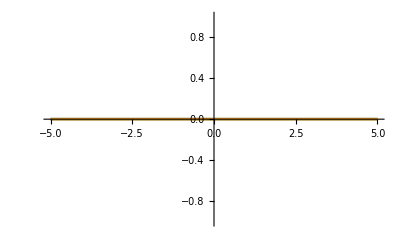

```mathematica
Plot[{-u0d[1.48,y] u1d[1.48,y],fxRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]+-u f1[t,K[1],y]K[1]1x]}

```mathematica
I
```

ⅈ

ξ can’t depend on x!

Export fx initial data

The source term goes to zero. The Vev is the first term and it is

```mathematica
(*1/NormCoeff*)Ayy vty z^4 E^(I k y)/(2 z^2)/.v->0/.k->2 Pi/L/.result//Re//Simplify
```

1/2 Re[Ayy ⅇ^((ⅈ π y)/5) vty z^2]

```mathematica
MaxValue[htxFunctionNonNormalised[zzz,0]//Abs,zzz>0&&zzz<1,zzz]
```

MaxValue[Abs[htxFunctionNonNormalised[zzz,0]],zzz>0&&zzz<1,zzz]

```mathematica
NormCoeff
```

0.1

```mathematica
htxNorm
```

htxNorm

```mathematica
1/8 z^4 (-ctx k^4-(cyx k^3+6 ⅈ vty) ω)/.ctx->0/.cyx->0
```

-3/4 ⅈ vty z^4 ω

```mathematica
fxData=Table[0(*(vty )1/2 NormCoeff  Ayy  E^(I k y)/htxNorm*)/.x->xValues[[i]]/.y->yValues[[j]]/.k->kn 2 Pi/L/.L->10/.result//Re,{i,1,xValues//Length},{j,1,yValues//Length}];
```

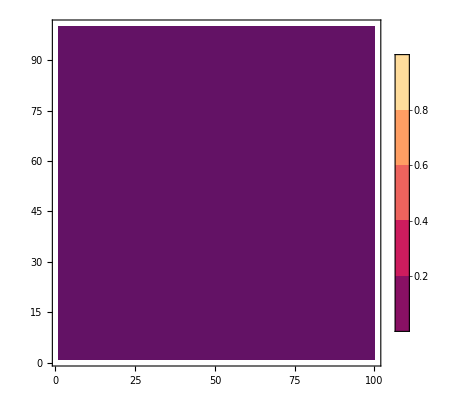

```mathematica
ListContourPlot[fxData//Transpose,PlotLegends->Automatic]
```

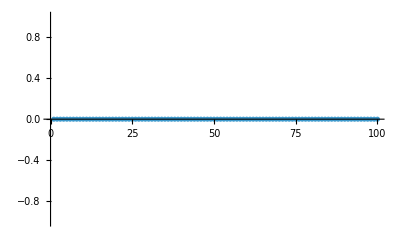

```mathematica
fxData[[1]]//ListPlot[#,PlotRange->All]&
```

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export[IDFolderName<>"Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1dInitialfx_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
F2ToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u2d[x,y];
```

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fyRule=Solve[Coefficient[F2ToMatch,ρ]==Coefficient[F2ExpOfρ,ρ],f2[t,z,y]]//Simplify
```

{{f2[t,z,y]→0}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

```mathematica
Plot[{-u0d[1.48,y] u2d[1.48,y],fyRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

-Graphics-

```mathematica
DSolve[SeriesCoefficient[F2ToMatch,{ρ,0,0}]==SeriesCoefficient[F2ExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,x]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fyData=Table[(*(vty )1/2 Axx NormCoeff  E^(I k x)/htxNorm*)0/.x->xValues[[i]]/.y->yValues[[j]]/.k->kn 2 Pi/L/.L->10/.result//Re,{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
result
```

{ϕvev→12.08495790317457930010330659033945317212768038838165609+22.31288488912226043126393800258587359585529701404252228 ⅈ,ω→3.161257027502500843228540046625393734814916374597929467-4.916417879672036112316239102195444071032629410176686264 ⅈ}

```mathematica
(*fxRule*)
```

```mathematica
Axx
```

Axx

```mathematica
fyData//Dimensions
```

{100,100}

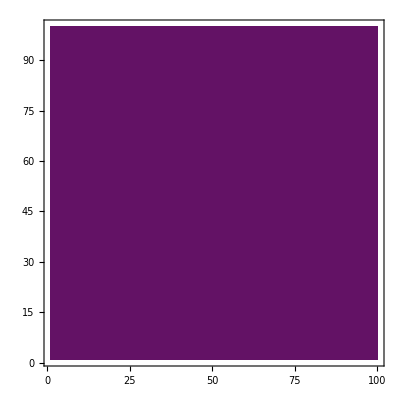

```mathematica
ListContourPlot[fyData//Transpose]
```

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export[IDFolderName<>"Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1dInitialfy_BBB.h5

```mathematica
"/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/VectorChannel_fund_kx1_A0d1_L10_0d1ui12_2uo24_N100_b1/VectorChannel_fund_kx1_A0d1_L10_0d1ui12_2uo24_N100_b1Initiala3_BBB.h5"
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/VectorChannel_fund_kx1_A0d1_L10_0d1ui12_2uo24_N100_b1/VectorChannel_fund_kx1_A0d1_L10_0d1ui12_2uo24_N100_b1Initiala3_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

### Bulk Functions

#### B Function

```mathematica
BulkFunctions
```

{S→-((1-a^2 u^6)^(1/4))/u,Gin→Log[(-√(1-a^2 u^6)-a u^3 √(1-a^2 u^6))/(-1+a^2 u^6)]/u^3,Bin→0}

```mathematica
ClearAll[InitialBAnalytic]
```

```mathematica
InitialBAnalytic[u_,x_,y_]:=0;
```

```mathematica
InitialBAnalytic[u,x,y]
```

0

```mathematica
InitialB1=Table[0(*(1+ (RandomReal[]-0.5)/100)*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.000402,Null}

```mathematica
InitialB=Table[0(*(1+(RandomReal[]-0.5)/100)*),{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
InitialB[[1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
(*InitialB[[1]]=InitialB[[2]];*)
```

{0.013391,Null}

```mathematica
InitialB//Dimensions
```

{58,100,100}

```mathematica
(*Table[InitialB[[1,i,j]]=-u1d[xValues[[i]],yValues[[j]]]^2/2,{i,1,xValues//Length},{j,1,yValues//Length}];*)
```

```mathematica
(*ListContourPlot[InitialB[[1]],PlotLegends->Automatic]*)
```

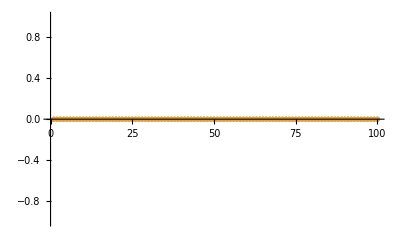

```mathematica
ListPlot[{InitialB[[1,1,;;]],Table[-u1d[xValues[[1]],yValues[[i]]]^2/2(*-InitialB[[1,1,i]]*),{i,1,yValues//Length}]}(*,Joined->True*)(*,PlotStyle->{Dashed,Dotted}*)]
```

```mathematica
(*phiFunc=InterpolatingFunction[…]*)
```

```mathematica
(*phi=Table[phiFunc[uValues[[i]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];*)
```

```mathematica
ExportData=Join[{InitialB(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.00011,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000026,Null}

```mathematica
Export[IDFolderName<>"InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1dInitialB_BBB.h5

#### G Function

```mathematica
BulkFunctions
```

{S→-((1-a^2 u^6)^(1/4))/u,Gin→Log[(-√(1-a^2 u^6)-a u^3 √(1-a^2 u^6))/(-1+a^2 u^6)]/u^3,Bin→0}

```mathematica
Series[Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4/.a->((*ⅇ^(ⅈ k x3)*)Cos[k x3])/2 vzx u^4/.k->kn 2 Pi/L,{u,0,10}](*/.result*)(*/.u->0*)(*//Normal*)
```

1/2 vzx Cos[(2 π x3)/L]+1/24 vzx^3 Cos[(2 π x3)/L]^3 u^8+O[u]^11

```mathematica
Series[Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^3/.a->((*ⅇ^(ⅈ k x3)*)Cos[k y])/2 vty u^4/.k->2 Pi/L,{u,0,10}](*/.result*)(*/.u->0*)(*//Normal*)
```

1/2 vty Cos[(π y)/5] u+1/24 vty^3 Cos[(π y)/5]^3 u^9+O[u]^11

```mathematica
Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==u^-2 a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}][[1]]/. C[1]->0/. C[2]->0/.C[3]->0
```

{S→-((1-a^2)^(1/6))/u,Gin→Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4,B1in→0,B2in→-Log[(1-a^2)^(1/6)]/u^4}

```mathematica
InitialG=Table[N[Log[(-√(1-a^2 u^6)-a u^3 √(1-a^2 u^6))/(-1+a^2 u^6)]/u^3/.a->Parametricgxy[uValues[[ui]],xValues[[xi]],yValues[[yi]]]/.u->uValues[[ui]](*/.y->yValues[[yi]]*)(*,$MinPrecision*)],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.020638285804663520718634386343135144524692689322666611088581989} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.043927822676104951760275252742384223896930682580977530188902328} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.063604851136622138137053904887562700011963908723723116287189654} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{17.3892,Null}

InterpolatingFunctio/ListPlotn::dmval :  Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
Series[Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4/.a->-(u^4 ω vzx)/k E^(I k y)/(2NormCoefff)(*/.result*),{u,0,2}]
```

-(ⅇ^(ⅈ k y) vzx ω)/(2 (k NormCoefff))+O[u]^3

```mathematica
Series[Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^4/.a->-(u^4 ω vzx)/k E^(I k y)/(2NormCoefff)(*/.result*),{u,0,2}]
```

```mathematica
(Series[Log[(-√(1-a^2)-a √(1-a^2))/(-1+a^2)]/u^3/.a->(ⅈ u^3 (0 k^4+0 k^3 ω+6 ⅈ vty ω))/(6 k)1/2 NormCoeff/hxyNorm(Ayyy  E^(I k y)+Axxx E^(I k x)),{u,0,4}]//Normal)/.u->0
```

-(0.51674 (Axxx ⅇ^(ⅈ k x)+Ayyy ⅇ^(ⅈ k y)) vty ω)/k

```mathematica
Series[Log[(-√(1-a^2 u^6)-a u^3 √(1-a^2 u^6))/(-1+a^2 u^6)]/u^3,{u,0,4}]
```

a+O[u]^5

```mathematica
Parametricgxy[uValues[[1]],xValues[[1]],yValues[[1]]]
```

0.0238123

```mathematica
InitialG1=Table[Parametricgxy[uValues[[1]],xValues[[1]],yValues[[1]]]/.result/.x->xValues[[i]]/.y->yValues[[j]]//Re,{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.037118,Null}

```mathematica
InitialG[[1]]=InitialG1;
```

```mathematica
IntFunctsG=Table[Interpolation[{uValues[[;;-4]],InitialG[[;;-4,1,j]]}//Transpose],{j,1,yValues//Length}];
```

```mathematica
Table[InitialG[[u,i,j]]=IntFunctsG[[j]][uValues[[u]]],{u,-4,-1},{i,1,xValues//Length},{j,1,yValues//Length}];
```

InterpolatingFunction::dmval: Input value {1.001563682871624339615963368402411826853266699211686314912310828} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ϕvev/.result
```

12.08495790317457930010330659033945317212768038838165609+22.31288488912226043126393800258587359585529701404252228 ⅈ

```mathematica
ListPlot3D[InitialG[[;;,1,;;]],PlotRange->All]
```

-Graphics3D-

```mathematica
ExportDataG=Join[{InitialG(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialG(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000114,Null}

```mathematica
ExportAttributesG=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataG=Table[ExportAttributesG[[i]]->ExportDataG[[i]],{i,1,ExportAttributesG//Length}];//AbsoluteTiming
```

{0.00002,Null}

```mathematica
Export[IDFolderName<>"InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1d/k0_o1_A0d1_L10_0d1ui12_2uo24_N100_b1dInitialG_BBB.h5